```mathematica
ClearAll["Global`*"]
(*Last Update: 11/06/2020*)
(*AndreHAM*)
```

von Neumann Entropy

#### Discussion -

For a given density matrix ρ the von Neumann entropy is defined as S[ρ]=-tr(ρln(ρ)):

Example:ρ=(1/4 | 0
0 | 3/4)

		S=-1/4Log[1/4]-3/4 Log[3/4]=0.562335

in Mathematica we write

S[σ_]:=-Tr[σ.MatrixLog[σ]]

obs.: Remember that we are dealing with matrices.

CAUTION: For mixed states there is no problem at all. However for pure states there is an important detail----> - 0Log[0]= indeterminate

to fix that we should specify that 0Log[0]=0

```mathematica
(* Demonstration *)
ρ=({{1/4, 0}, {0, 3/4}});
σ=({{1, 0}, {0, 0}});

S[ρ_]:=-Tr[ρ.MatrixLog[ρ]];

S[ρ]//N
```

0.562335

```mathematica
S[σ]
```

MatrixLog::fnand: The function Log is not analytic or defined at 0.

-Tr[{{1,0},{0,0}}.MatrixLog[{{1,0},{0,0}}]]

Behaviour for a 2 - level system -

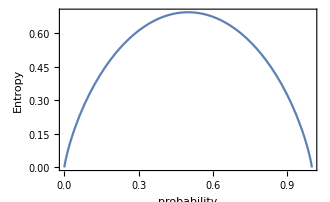

```mathematica
Plot[-p Log[p]-(1-p) Log[(1-p)],{p,0,1}, FrameLabel->{"probability","Entropy"}]
```

#### Entropy function -

```mathematica
(* As a default we will assume that any number of the order of 10^(-10) is essentially zero (I am using the same threshold of the Chop[] function ) *)
OrderOfMagnitude[x_]:=Floor@Log[10,Abs[x]];

SvN[ρ_]:=Sum[If[OrderOfMagnitude[Eigenvalues[ρ][[i]]]>-10,(-Eigenvalues[ρ][[i]]Log[Eigenvalues[ρ][[i]]]),0],{i,1,Length@Eigenvalues[ρ]}];

(* Notice that for any eigenvalue with order of magnitude less than -10 is discarted from the sum *)
```

Simple tests -

```mathematica
ρ1=({{1/4, 0}, {0, 3/4}});
ρ2=({{1/9, 0}, {0, 8/9}});
ρ3=({{1/2, 0, 0}, {0, 1/2, 0}, {0, 0, 0}});
ρ4=({{1/7, 0, 0}, {0, 4/7, 0}, {0, 0, 2/7}});
ρ5=({{1/3, 0, 0}, {0, 1/3, 0}, {0, 0, 1/3}});

SvN[ρ1]//N
SvN[ρ2]//N
SvN[ρ3]//N
SvN[ρ4]//N
SvN[ρ5] (* Equally  distributed state*)
```

0.562335

0.348832

0.693147

0.9557

Log[3]